# Model T1-3-B-α = 0 - scalar2g

## Fig. 7.1

Read File

## Read micrOMEGA output file

The output parameters from micrOMEGA are:
{λ_4, λ_5, λ_1^(1,1), λ_1^(1,2), λ_1^(2,1), λ_1^(2,2), λ_6^(1,1), λ_6^(1,2), λ_6^(2,1), λ_6^(2,2), λ_6^(3,1), λ_6^(3,2), m_(⋁_1), m_(⋁_2), m_(⋁_3), M_H, (M_(ϕ^2))^(1,1), (M_(ϕ^2))^(1,2), (M_(ϕ^2))^(2,1), (M_(ϕ^2))^(2,2), M_Ψ, M_ψψ, m_ψ, m_χ_1, m_χ_2, m_χ_3, M_DM, σ_SI, σ_SD, Ω_DM h^2}

```mathematica
Output = Module[{filename,nparameters,temp},
SetDirectory[NotebookDirectory[]];
filename="Fig7.1_scan.out";
nparameters = 30;
temp=ReadList[filename,Number];
Table[temp⟦i;;i+29⟧,{i,1,Length[temp],nparameters}]
 ];
```

## Show parameters table

Print parameter table

```mathematica
TableForm[Join[{{"λ_4","λ_5","λ_1^(1, 1)","λ_1^(1, 2)","λ_1^(2, 1)","λ_1^(2, 2)","λ_6^(1, 1)","λ_6^(1, 2)","λ_6^(2, 1)","λ_6^(2, 2)","λ_6^(3, 1)","λ_6^(3, 2)","m_(⋁_1)","m_(⋁_2)","m_(⋁_3)","M_H","(M_(ϕ^2))^(1, 1)","(M_(ϕ^2))^(1, 2)","(M_(ϕ^2))^(2, 1)","(M_(ϕ^2))^(2, 2)","M_Ψ","M_ψψ","m_ψ","m_χ_1","m_χ_2","m_χ_3","M_DM","σ_SI","σ_SD","Ω_DMh^2"}},Output]]
```

λ_4 | λ_5 | λ_1^(1, 1) | λ_1^(1, 2) | λ_1^(2, 1) | λ_1^(2, 2) | λ_6^(1, 1) | λ_6^(1, 2) | λ_6^(2, 1) | λ_6^(2, 2) | λ_6^(3, 1) | λ_6^(3, 2) | m_(⋁_1) | m_(⋁_2) | m_(⋁_3) | M_H | (M_(ϕ^2))^(1, 1) | (M_(ϕ^2))^(1, 2) | (M_(ϕ^2))^(2, 1) | (M_(ϕ^2))^(2, 2) | M_Ψ | M_ψψ | m_ψ | m_χ_1 | m_χ_2 | m_χ_3 | M_DM | σ_SI | σ_SD | Ω_DMh^2
-0.5 | 0.36 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 127.22 | 1.×10^6 | 0. | 0. | 1.×10^6 | 200. | 300. | 299.552 | 217.94 | 302.823 | 321.414 | 217.94 | 5.64398×10^-9 | 0.000267953 | 0.0541088
-0.49 | 0.36 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 127.237 | 1.×10^6 | 0. | 0. | 1.×10^6 | 200. | 300. | 299.558 | 217.95 | 302.336 | 320.926 | 217.95 | 5.72024×10^-9 | 0.000228775 | 0.0625287
-0.48 | 0.36 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 127.252 | 1.×10^6 | 0. | 0. | 1.×10^6 | 200. | 300. | 299.565 | 217.93 | 301.885 | 320.443 | 217.93 | 5.7745×10^-9 | 0.000192701 | 0.0730741
-0.47 | 0.36 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 127.266 | 1.×10^6 | 0. | 0. | 1.×10^6 | 200. | 300. | 299.571 | 217.88 | 301.468 | 319.965 | 217.88 | 5.80547×10^-9 | 0.000159797 | 0.0864738
-0.46 | 0.36 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 127.279 | 1.×10^6 | 0. | 0. | 1.×10^6 | 200. | 300. | 299.577 | 217.799 | 301.088 | 319.492 | 217.799 | 5.81209×10^-9 | 0.000130101 | 0.103789
-0.45 | 0.36 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 127.292 | 1.×10^6 | 0. | 0. | 1.×10^6 | 200. | 300. | 299.583 | 217.687 | 300.743 | 319.024 | 217.687 | 5.79357×10^-9 | 0.00010363 | 0.126571
-0.44 | 0.36 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 127.303 | 1.×10^6 | 0. | 0. | 1.×10^6 | 200. | 300. | 299.588 | 217.544 | 300.435 | 318.561 | 217.544 | 5.74938×10^-9 | 0.0000803718 | 0.157156
-0.43 | 0.36 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 127.313 | 1.×10^6 | 0. | 0. | 1.×10^6 | 200. | 300. | 299.593 | 217.368 | 300.163 | 318.103 | 217.368 | 5.67932×10^-9 | 0.0000602886 | 0.199261
-0.42 | 0.36 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 127.323 | 1.×10^6 | 0. | 0. | 1.×10^6 | 200. | 300. | 299.599 | 217.161 | 299.929 | 317.65 | 217.161 | 5.58353×10^-9 | 0.0000433152 | 0.258082
-0.41 | 0.36 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 127.332 | 1.×10^6 | 0. | 0. | 1.×10^6 | 200. | 300. | 299.603 | 216.923 | 299.731 | 317.201 | 216.923 | 5.46248×10^-9 | 0.0000293598 | 0.342565
-0.4 | 0.36 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 127.34 | 1.×10^6 | 0. | 0. | 1.×10^6 | 200. | 300. | 299.608 | 216.652 | 299.57 | 316.758 | 216.652 | 5.31697×10^-9 | 0.0000183057 | 0.465274
-0.39 | 0.36 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 127.347 | 1.×10^6 | 0. | 0. | 1.×10^6 | 200. | 300. | 299.612 | 216.349 | 299.447 | 316.319 | 216.349 | 5.14815×10^-9 | 0.0000100123 | 0.641448
-0.38 | 0.36 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 127.354 | 1.×10^6 | 0. | 0. | 1.×10^6 | 200. | 300. | 299.616 | 216.015 | 299.36 | 315.886 | 216.015 | 4.95749×10^-9 | 4.31879×10^-6 | 0.877025
-0.37 | 0.36 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 127.36 | 1.×10^6 | 0. | 0. | 1.×10^6 | 200. | 300. | 299.62 | 215.65 | 299.309 | 315.457 | 215.65 | 4.74675×10^-9 | 1.04592×10^-6 | 1.13188
-0.36 | 0.36 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 127.366 | 1.×10^6 | 0. | 0. | 1.×10^6 | 200. | 300. | 299.623 | 215.254 | 299.294 | 315.034 | 215.254 | 4.51796×10^-9 | 0. | 1.28659
-0.35 | 0.36 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 127.371 | 1.×10^6 | 0. | 0. | 1.×10^6 | 200. | 300. | 299.627 | 214.827 | 299.315 | 314.616 | 214.827 | 4.27338×10^-9 | 9.76115×10^-7 | 1.23751
-0.34 | 0.36 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 127.376 | 1.×10^6 | 0. | 0. | 1.×10^6 | 200. | 300. | 299.63 | 214.37 | 299.372 | 314.203 | 214.37 | 4.01548×10^-9 | 3.76179×10^-6 | 1.04101
-0.33 | 0.36 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 127.38 | 1.×10^6 | 0. | 0. | 1.×10^6 | 200. | 300. | 299.632 | 213.884 | 299.462 | 313.794 | 213.884 | 3.74687×10^-9 | 8.14056×10^-6 | 0.820868
-0.32 | 0.36 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 127.384 | 1.×10^6 | 0. | 0. | 1.×10^6 | 200. | 300. | 299.635 | 213.369 | 299.587 | 313.391 | 213.369 | 3.47027×10^-9 | 0.0000138955 | 0.639411
-0.31 | 0.36 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 127.387 | 1.×10^6 | 0. | 0. | 1.×10^6 | 200. | 300. | 299.637 | 212.826 | 299.745 | 312.993 | 212.826 | 3.18848×10^-9 | 0.0000208122 | 0.504798
-0.3 | 0.36 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 127.39 | 1.×10^6 | 0. | 0. | 1.×10^6 | 200. | 300. | 299.639 | 212.255 | 299.936 | 312.601 | 212.255 | 2.90432×10^-9 | 0.0000286822 | 0.407488
-0.29 | 0.36 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 127.393 | 1.×10^6 | 0. | 0. | 1.×10^6 | 200. | 300. | 299.64 | 211.658 | 300.158 | 312.213 | 211.658 | 2.6206×10^-9 | 0.0000373048 | 0.336965
-0.28 | 0.36 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 127.396 | 1.×10^6 | 0. | 0. | 1.×10^6 | 200. | 300. | 299.641 | 211.034 | 300.411 | 311.831 | 211.034 | 2.34008×10^-9 | 0.0000464898 | 0.2849
-0.27 | 0.36 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 127.398 | 1.×10^6 | 0. | 0. | 1.×10^6 | 200. | 300. | 299.642 | 210.386 | 300.695 | 311.453 | 210.386 | 2.06545×10^-9 | 0.0000560592 | 0.245777
-0.26 | 0.36 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 127.4 | 1.×10^6 | 0. | 0. | 1.×10^6 | 200. | 300. | 299.643 | 209.714 | 301.006 | 311.081 | 209.714 | 1.7993×10^-9 | 0.0000658478 | 0.215916
-0.25 | 0.36 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 127.401 | 1.×10^6 | 0. | 0. | 1.×10^6 | 200. | 300. | 299.643 | 209.018 | 301.347 | 310.714 | 209.018 | 1.54407×10^-9 | 0.0000757051 | 0.192682
-0.24 | 0.36 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 127.403 | 1.×10^6 | 0. | 0. | 1.×10^6 | 200. | 300. | 299.643 | 208.3 | 301.718 | 310.353 | 208.3 | 1.30208×10^-9 | 0.000085495 | 0.174348
-0.23 | 0.36 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 127.404 | 1.×10^6 | 0. | 0. | 1.×10^6 | 200. | 300. | 299.643 | 207.56 | 302.117 | 309.996 | 207.56 | 1.07548×10^-9 | 0.0000950963 | 0.159695
-0.22 | 0.36 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 127.405 | 1.×10^6 | 0. | 0. | 1.×10^6 | 200. | 300. | 299.642 | 206.799 | 302.541 | 309.645 | 206.799 | 8.66264×10^-10 | 0.000104403 | 0.1479
-0.21 | 0.36 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 127.406 | 1.×10^6 | 0. | 0. | 1.×10^6 | 200. | 300. | 299.641 | 206.019 | 302.991 | 309.299 | 206.019 | 6.76241×10^-10 | 0.000113322 | 0.138331
-0.2 | 0.36 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 127.407 | 1.×10^6 | 0. | 0. | 1.×10^6 | 200. | 300. | 299.64 | 205.219 | 303.465 | 308.959 | 205.219 | 5.07055×10^-10 | 0.000121776 | 0.130525
-0.19 | 0.36 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 127.407 | 1.×10^6 | 0. | 0. | 1.×10^6 | 200. | 300. | 299.638 | 204.401 | 303.962 | 308.624 | 204.401 | 3.60178×10^-10 | 0.000129699 | 0.124151
-0.18 | 0.36 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 127.408 | 1.×10^6 | 0. | 0. | 1.×10^6 | 200. | 300. | 299.636 | 203.566 | 304.482 | 308.294 | 203.566 | 2.37322×10^-10 | 0.000137039 | 0.118957
-0.17 | 0.36 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 127.408 | 1.×10^6 | 0. | 0. | 1.×10^6 | 200. | 300. | 299.634 | 202.714 | 305.025 | 307.969 | 202.714 | 1.38396×10^-10 | 0.000143754 | 0.114739
-0.16 | 0.36 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 127.408 | 1.×10^6 | 0. | 0. | 1.×10^6 | 200. | 300. | 299.632 | 201.846 | 305.588 | 307.65 | 201.846 | 6.5616×10^-11 | 0.000149814 | 0.111354
-0.15 | 0.36 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 127.408 | 1.×10^6 | 0. | 0. | 1.×10^6 | 200. | 300. | 299.629 | 200.963 | 306.172 | 307.336 | 200.963 | 1.94069×10^-11 | 0.000155195 | 0.108687
-0.14 | 0.36 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 127.408 | 1.×10^6 | 0. | 0. | 1.×10^6 | 200. | 300. | 299.626 | 200.066 | 306.775 | 307.028 | 200.066 | 4.67351×10^-13 | 0.000159886 | 0.106647
-0.13 | 0.36 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 127.408 | 1.×10^6 | 0. | 0. | 1.×10^6 | 200. | 300. | 299.623 | 199.155 | 306.724 | 307.397 | 199.155 | 9.3653×10^-12 | 0.00016388 | 0.105165
-0.12 | 0.36 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 127.408 | 1.×10^6 | 0. | 0. | 1.×10^6 | 200. | 300. | 299.619 | 198.231 | 306.427 | 308.038 | 198.231 | 4.65395×10^-11 | 0.000167179 | 0.104186
-0.11 | 0.36 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 127.408 | 1.×10^6 | 0. | 0. | 1.×10^6 | 200. | 300. | 299.615 | 197.295 | 306.135 | 308.696 | 197.295 | 1.12521×10^-10 | 0.000169788 | 0.103671
-0.1 | 0.36 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 127.407 | 1.×10^6 | 0. | 0. | 1.×10^6 | 200. | 300. | 299.611 | 196.347 | 305.848 | 309.371 | 196.347 | 2.06913×10^-10 | 0.000171721 | 0.103586
-0.09 | 0.36 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 127.407 | 1.×10^6 | 0. | 0. | 1.×10^6 | 200. | 300. | 299.607 | 195.388 | 305.567 | 310.062 | 195.388 | 3.30467×10^-10 | 0.000172993 | 0.103911
-0.08 | 0.36 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 127.406 | 1.×10^6 | 0. | 0. | 1.×10^6 | 200. | 300. | 299.602 | 194.419 | 305.291 | 310.769 | 194.419 | 4.83028×10^-10 | 0.000173624 | 0.104631
-0.07 | 0.36 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 127.405 | 1.×10^6 | 0. | 0. | 1.×10^6 | 200. | 300. | 299.597 | 193.441 | 305.021 | 311.491 | 193.441 | 6.64572×10^-10 | 0.000173636 | 0.105736
-0.06 | 0.36 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 127.404 | 1.×10^6 | 0. | 0. | 1.×10^6 | 200. | 300. | 299.592 | 192.452 | 304.756 | 312.228 | 192.452 | 8.75009×10^-10 | 0.000173055 | 0.107225
-0.05 | 0.36 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 127.403 | 1.×10^6 | 0. | 0. | 1.×10^6 | 200. | 300. | 299.587 | 191.455 | 304.497 | 312.978 | 191.455 | 1.11612×10^-9 | 0.000171909 | 0.1091
-0.04 | 0.36 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 127.402 | 1.×10^6 | 0. | 0. | 1.×10^6 | 200. | 300. | 299.582 | 190.45 | 304.244 | 313.741 | 190.45 | 1.38595×10^-9 | 0.000170226 | 0.111369
-0.03 | 0.36 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 127.401 | 1.×10^6 | 0. | 0. | 1.×10^6 | 200. | 300. | 299.576 | 189.437 | 303.996 | 314.516 | 189.437 | 1.68312×10^-9 | 0.000168037 | 0.114043
-0.02 | 0.36 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 127.399 | 1.×10^6 | 0. | 0. | 1.×10^6 | 200. | 300. | 299.57 | 188.417 | 303.754 | 315.295 | 188.417 | 2.00852×10^-9 | 0.000165372 | 0.117137
-0.01 | 0.36 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 127.398 | 1.×10^6 | 0. | 0. | 1.×10^6 | 200. | 300. | 299.564 | 187.39 | 303.517 | 316.1 | 187.39 | 2.36182×10^-9 | 0.000162264 | 0.120677

Plot

## Raw

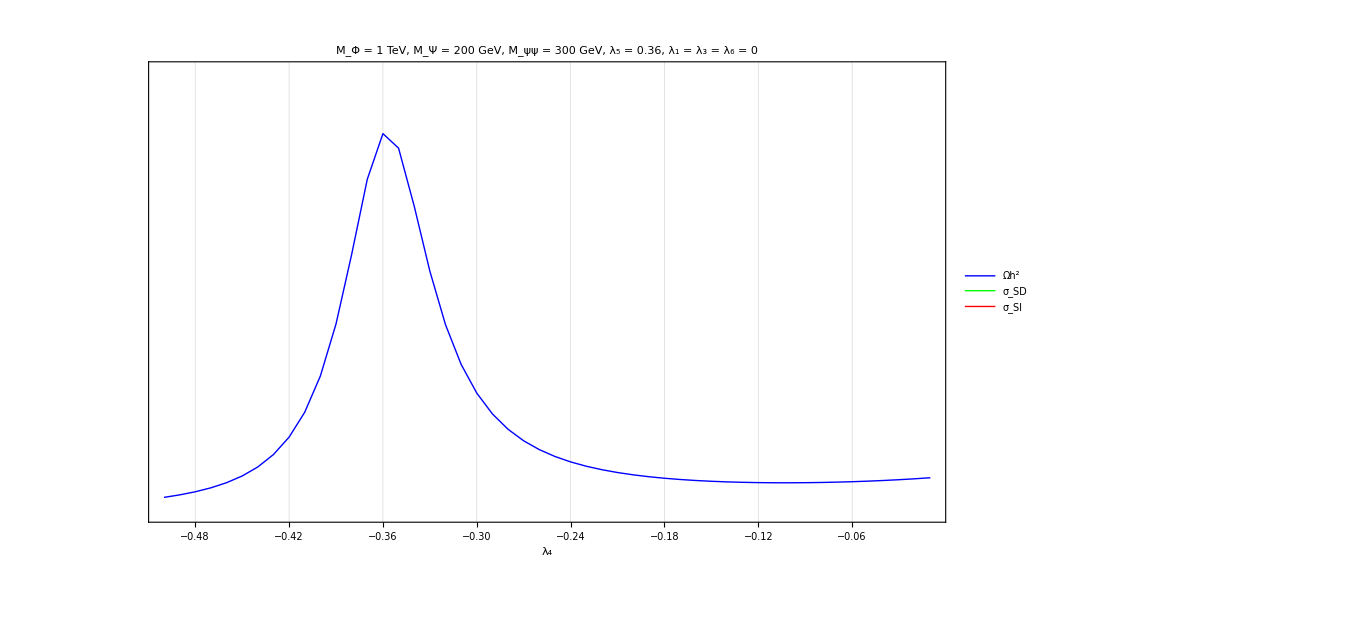

```mathematica
Block[
{label=Style["",24,SingleLetterItalics->False],
legend,
color={Blue,Green,Red},
Ω
},
legend=TableForm[
{{Graphics[{color⟦1⟧,Thick,Line[{{0,0},{100,0}}]},ImageSize->{40,10}],
Style["Ωh^2",24,SingleLetterItalics->False]},
{Graphics[{color⟦2⟧,Thick,Line[{{0,0},{100,0}}]},ImageSize->{40,10}],
Style["σ_SD",24,SingleLetterItalics->False]},
{Graphics[{color⟦3⟧,Thick,Line[{{0,0},{100,0}}]},ImageSize->{40,10}],
Style["σ_SI",24,SingleLetterItalics->False]}
}];

Ω = Table[{Output⟦i,1⟧,Output⟦i,30⟧},{i,1,Length[Output]}];

ListPlot[{Ω}//Evaluate,
Joined->True,
PlotRange->{{Output⟦1,1⟧,Output⟦Length[Output],1⟧},{0,1.5}},
PlotStyle->{{color⟦1⟧,Thick}},
ImageSize->1000,
GridLines->Automatic,
PlotLabel->Style["M_Φ = 1 TeV, M_Ψ = 200 GeV, M_ψψ = 300 GeV, λ_5 = 0.36, λ_1 = λ_3 = λ_6 = 0",FontSize->30],
FrameLabel->{{None,"Ωh^2"},{"λ_4", None}},
FrameTicks->{{None,All},{All,None}},
LabelStyle->24,
Frame->True,
Epilog->{Inset[legend,Scaled[{0.05,0.05}],{Left,Bottom}]}
]
]
```

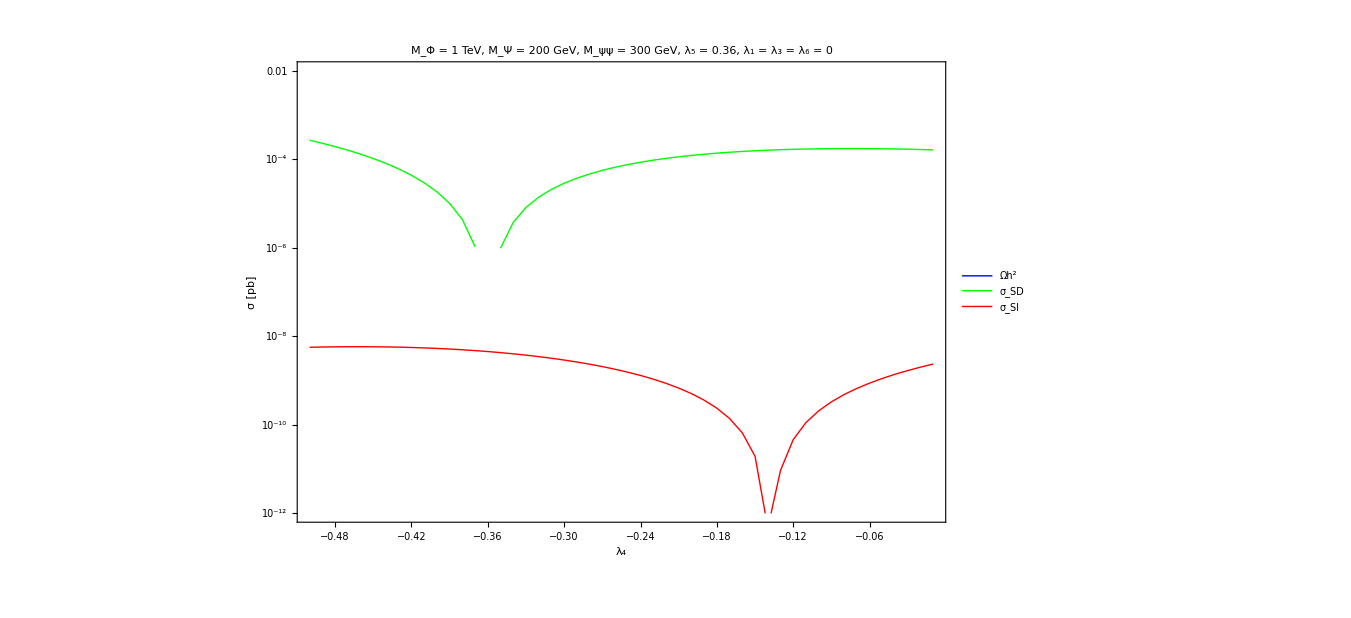

```mathematica
Block[
{label=Style["",24,SingleLetterItalics->False],
legend,
color={Blue,Green,Red},
σSD,σSI
},
legend=TableForm[
{{Graphics[{color⟦1⟧,Thick,Line[{{0,0},{100,0}}]},ImageSize->{40,10}],
Style["Ωh^2",24,SingleLetterItalics->False]},
{Graphics[{color⟦2⟧,Thick,Line[{{0,0},{100,0}}]},ImageSize->{40,10}],
Style["σ_SD",24,SingleLetterItalics->False]},
{Graphics[{color⟦3⟧,Thick,Line[{{0,0},{100,0}}]},ImageSize->{40,10}],
Style["σ_SI",24,SingleLetterItalics->False]}
}];

σSD = Table[{Output⟦i,1⟧,Output⟦i,29⟧},{i,1,Length[Output]}];
σSI = Table[{Output⟦i,1⟧,Output⟦i,28⟧},{i,1,Length[Output]}];

ListLogPlot[{σSD,σSI}//Evaluate,
Joined->True,
PlotRange->{{Output⟦1,1⟧,Output⟦Length[Output],1⟧},{10^-12,10^-2}},
PlotStyle->{{color⟦2⟧,Thick},{color⟦3⟧,Thick}},
ImageSize->1000,
GridLines->Automatic,
PlotLabel->Style["M_Φ = 1 TeV, M_Ψ = 200 GeV, M_ψψ = 300 GeV, λ_5 = 0.36, λ_1 = λ_3 = λ_6 = 0",FontSize->30],
FrameLabel->{{"σ [pb]",None},{"λ_4", None}},
FrameTicks->{{All,None},{All,None}},
LabelStyle->24,
Frame->True,
Epilog->{Inset[legend,Scaled[{0.05,0.05}],{Left,Bottom}]}
]
]
```

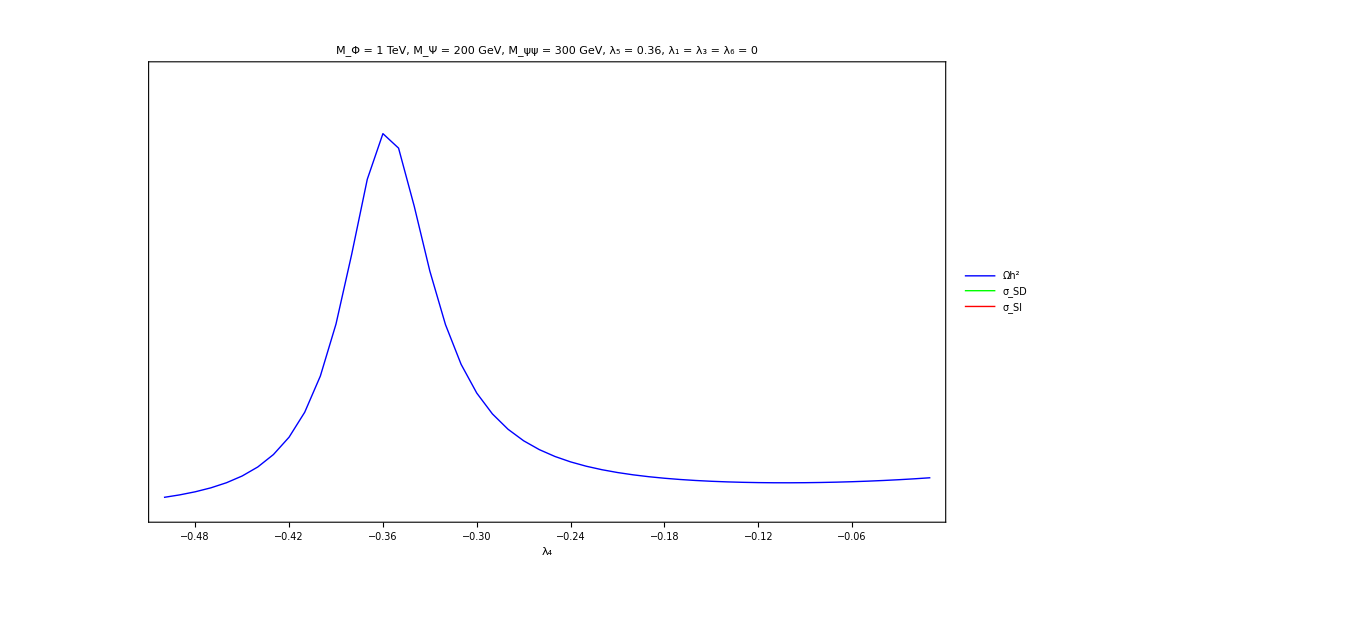
-Graphics--Graphics-

```mathematica
Block[
{label=Style["",24,SingleLetterItalics->False],
legend,
color={Blue,Green,Red},
Relic,Ω,
DirectDetection,σSD,σSI
},
legend=TableForm[
{{Graphics[{color⟦1⟧,Thick,Line[{{0,0},{100,0}}]},ImageSize->{40,10}],
Style["Ωh^2",24,SingleLetterItalics->False]},
{Graphics[{color⟦2⟧,Thick,Line[{{0,0},{100,0}}]},ImageSize->{40,10}],
Style["σ_SD",24,SingleLetterItalics->False]},
{Graphics[{color⟦3⟧,Thick,Line[{{0,0},{100,0}}]},ImageSize->{40,10}],
Style["σ_SI",24,SingleLetterItalics->False]}
}];

Ω = Table[{Output⟦i,1⟧,Output⟦i,30⟧},{i,1,Length[Output]}];
σSD = Table[{Output⟦i,1⟧,Output⟦i,29⟧},{i,1,Length[Output]}];
σSI = Table[{Output⟦i,1⟧,Output⟦i,28⟧},{i,1,Length[Output]}];

Relic=ListPlot[{Ω}//Evaluate,
Joined->True,
PlotRange->{{Output⟦1,1⟧,Output⟦Length[Output],1⟧},{0,1.5}},
PlotStyle->{{color⟦1⟧,Thick}},
ImageSize->1000,
(*GridLines->Automatic,*)
PlotLabel->Style["M_Φ = 1 TeV, M_Ψ = 200 GeV, M_ψψ = 300 GeV, λ_5 = 0.36, λ_1 = λ_3 = λ_6 = 0",FontSize->30],
FrameLabel->{{None,"Ωh^2"},{"λ_4", None}},
FrameTicks->{{None,All},{All,None}},
LabelStyle->24,
ImagePadding->100,
Frame->True,
Epilog->{Inset[legend,Scaled[{0.05,0.05}],{Left,Bottom}]}
];
DirectDetection = ListLogPlot[{σSD,σSI}//Evaluate,
Joined->True,
PlotRange->{{Output⟦1,1⟧,Output⟦Length[Output],1⟧},{10^-12,10^-2}},
PlotStyle->{{color⟦2⟧,Thick},{color⟦3⟧,Thick}},
ImageSize->1000,
(*GridLines->Automatic,*)
PlotLabel->Style["M_Φ = 1 TeV, M_Ψ = 200 GeV, M_ψψ = 300 GeV, λ_5 = 0.36, λ_1 = λ_3 = λ_6 = 0",FontSize->30],
FrameLabel->{{"σ [pb]",None},{"λ_4", None}},
FrameTicks->{{All,None},{All,None}},
LabelStyle->24,
ImagePadding->100,
Frame->True,
Epilog->{Inset[legend,Scaled[{0.05,0.05}],{Left,Bottom}]}
];
Overlay[{Relic,DirectDetection}]
]
```

## Interpolation

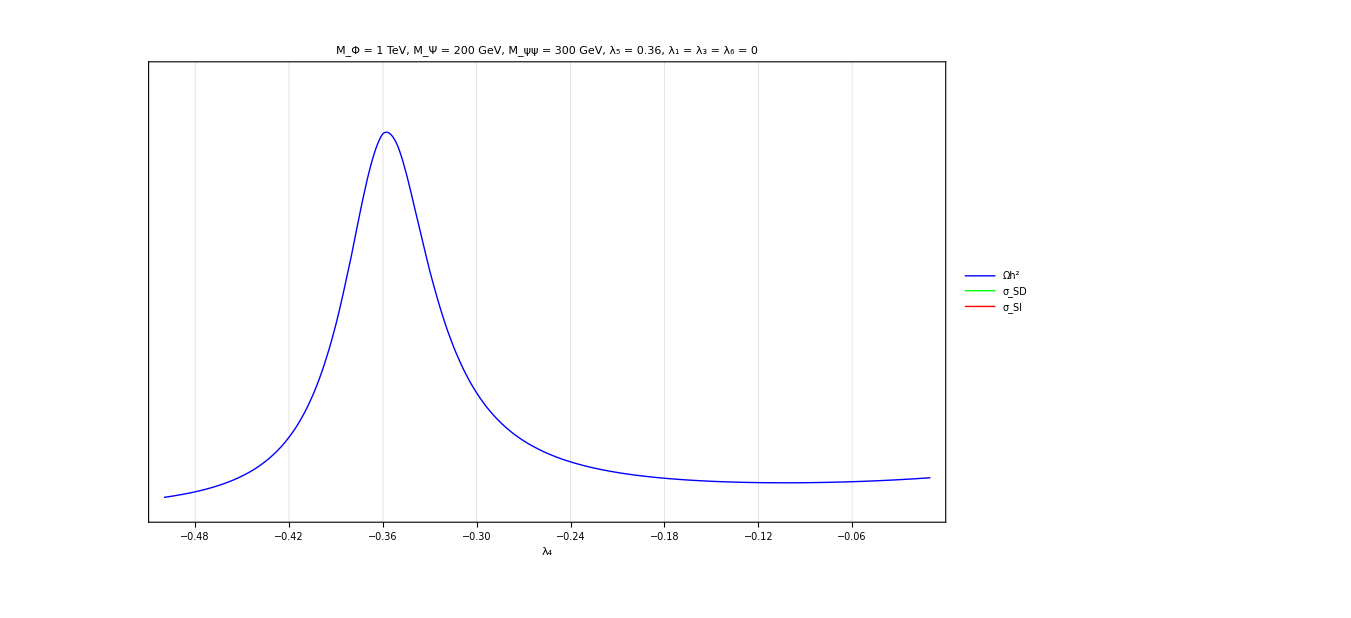

```mathematica
Block[
{label=Style["",24,SingleLetterItalics->False],
legend,
color={Blue,Green,Red},
Ω
},
legend=TableForm[
{{Graphics[{color⟦1⟧,Thick,Line[{{0,0},{100,0}}]},ImageSize->{40,10}],
Style["Ωh^2",24,SingleLetterItalics->False]},
{Graphics[{color⟦2⟧,Thick,Line[{{0,0},{100,0}}]},ImageSize->{40,10}],
Style["σ_SD",24,SingleLetterItalics->False]},
{Graphics[{color⟦3⟧,Thick,Line[{{0,0},{100,0}}]},ImageSize->{40,10}],
Style["σ_SI",24,SingleLetterItalics->False]}
}];

Ω = Interpolation[Table[{Output⟦i,1⟧,Output⟦i,30⟧},{i,1,Length[Output]}],InterpolationOrder->3][λ4];

Plot[{Ω}//Evaluate,{λ4,Output⟦1,1⟧,Output⟦Length[Output],1⟧},
PlotRange->{{Output⟦1,1⟧,Output⟦Length[Output],1⟧},{0,1.5}},
PlotStyle->{{color⟦1⟧,Thick}},
ImageSize->1000,
GridLines->Automatic,
PlotLabel->Style["M_Φ = 1 TeV, M_Ψ = 200 GeV, M_ψψ = 300 GeV, λ_5 = 0.36, λ_1 = λ_3 = λ_6 = 0",FontSize->30],
FrameLabel->{{None,"Ωh^2"},{"λ_4", None}},
FrameTicks->{{None,All},{All,None}},
LabelStyle->24,
Frame->True,
Epilog->{Inset[legend,Scaled[{0.05,0.05}],{Left,Bottom}]}
]
]
```

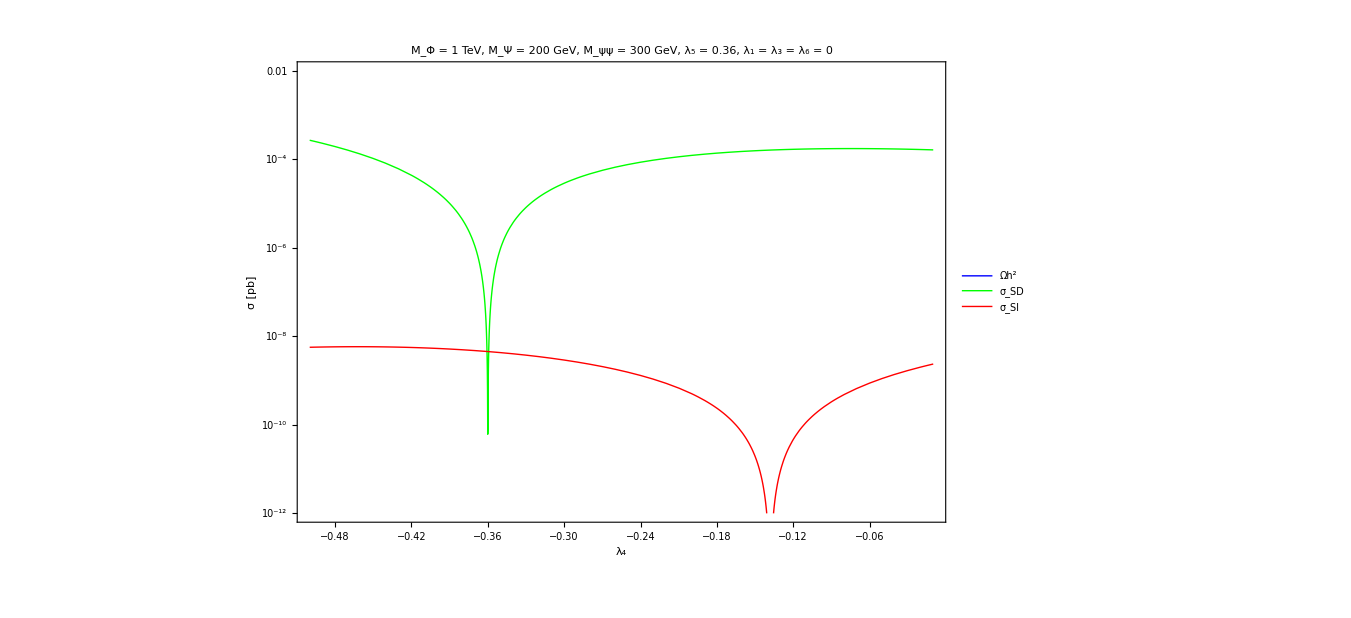

```mathematica
Block[
{label=Style["",24,SingleLetterItalics->False],
legend,
color={Blue,Green,Red},
σSD,σSI
},
legend=TableForm[
{{Graphics[{color⟦1⟧,Thick,Line[{{0,0},{100,0}}]},ImageSize->{40,10}],
Style["Ωh^2",24,SingleLetterItalics->False]},
{Graphics[{color⟦2⟧,Thick,Line[{{0,0},{100,0}}]},ImageSize->{40,10}],
Style["σ_SD",24,SingleLetterItalics->False]},
{Graphics[{color⟦3⟧,Thick,Line[{{0,0},{100,0}}]},ImageSize->{40,10}],
Style["σ_SI",24,SingleLetterItalics->False]}
}];

σSD = Interpolation[Table[{Output⟦i,1⟧,Output⟦i,29⟧},{i,1,Length[Output]}],InterpolationOrder->3][λ4];
σSI = Interpolation[Table[{Output⟦i,1⟧,Output⟦i,28⟧},{i,1,Length[Output]}],InterpolationOrder->3][λ4];

LogPlot[{σSD,σSI}//Evaluate,{λ4,Output⟦1,1⟧,Output⟦Length[Output],1⟧},
PlotRange->{{Output⟦1,1⟧,Output⟦Length[Output],1⟧},{10^-12,10^-2}},
PlotStyle->{{color⟦2⟧,Thick},{color⟦3⟧,Thick}},
ImageSize->1000,
GridLines->Automatic,
PlotLabel->Style["M_Φ = 1 TeV, M_Ψ = 200 GeV, M_ψψ = 300 GeV, λ_5 = 0.36, λ_1 = λ_3 = λ_6 = 0",FontSize->30],
FrameLabel->{{"σ [pb]",None},{"λ_4", None}},
FrameTicks->{{All,None},{All,None}},
LabelStyle->24,
Frame->True,
Epilog->{Inset[legend,Scaled[{0.05,0.05}],{Left,Bottom}]}
]
]
```

## Merging

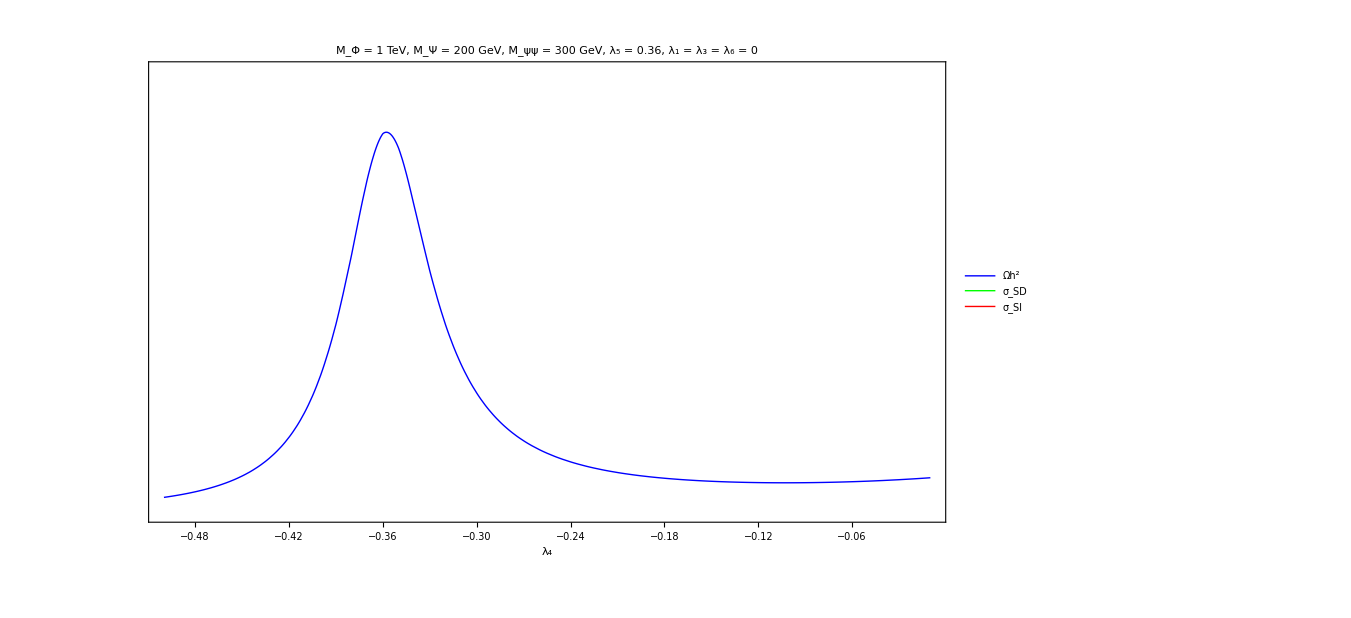
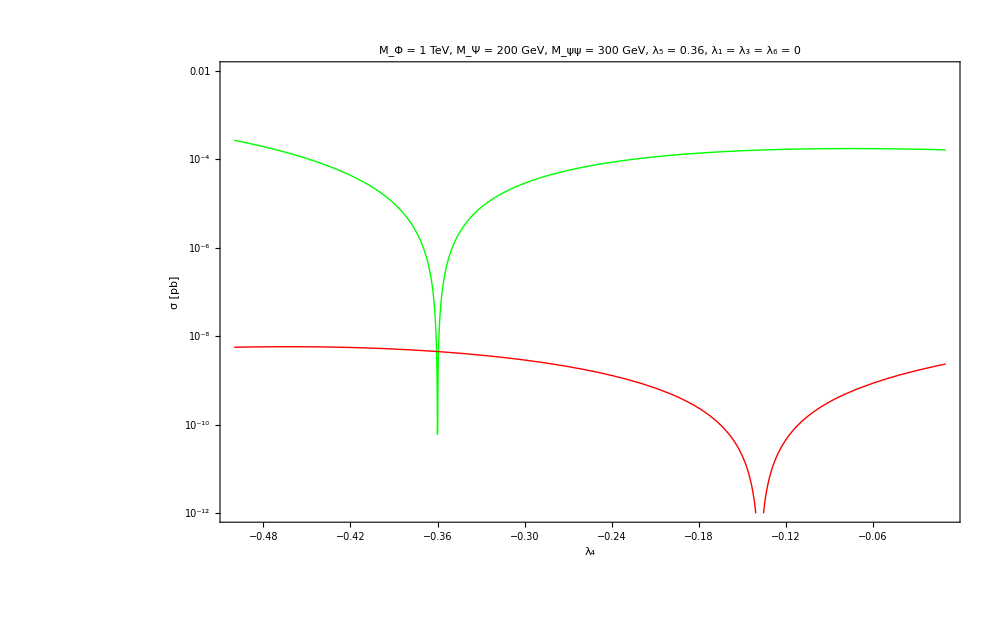

```mathematica
Block[
{label=Style["",24,SingleLetterItalics->False],
legend,
color={Blue,Green,Red},
Relic,Ω,
DirectDetection,σSD,σSI,
padding,plotlabel,epilog
},
legend=TableForm[
{{Graphics[{color⟦1⟧,Thick,Line[{{0,0},{100,0}}]},ImageSize->{40,10}],
Style["Ωh^2",24,SingleLetterItalics->False]},
{Graphics[{color⟦2⟧,Thick,Line[{{0,0},{100,0}}]},ImageSize->{40,10}],
Style["σ_SD",24,SingleLetterItalics->False]},
{Graphics[{color⟦3⟧,Thick,Line[{{0,0},{100,0}}]},ImageSize->{40,10}],
Style["σ_SI",24,SingleLetterItalics->False]}
}];
padding={{100, 100}, {100,Automatic}};
plotlabel=Style["M_Φ = 1 TeV, M_Ψ = 200 GeV, M_ψψ = 300 GeV, λ_5 = 0.36, λ_1 = λ_3 = λ_6 = 0",FontSize->30];
epilog ={Inset[legend,Scaled[{0.95,0.50}],{Right,Bottom}]};

Ω = Interpolation[Table[{Output⟦i,1⟧,Output⟦i,30⟧},{i,1,Length[Output]}],InterpolationOrder->3][λ4];
σSD = Interpolation[Table[{Output⟦i,1⟧,Output⟦i,29⟧},{i,1,Length[Output]}],InterpolationOrder->3][λ4];
σSI = Interpolation[Table[{Output⟦i,1⟧,Output⟦i,28⟧},{i,1,Length[Output]}],InterpolationOrder->3][λ4];

Relic=Plot[{Ω}//Evaluate,{λ4,Output⟦1,1⟧,Output⟦Length[Output],1⟧},
PlotRange->{{Output⟦1,1⟧,Output⟦Length[Output],1⟧},{0,1.5}},
PlotStyle->{{color⟦1⟧,Thick}},
ImageSize->1000,
(*GridLines->Automatic,*)
PlotLabel->plotlabel,
FrameLabel->{{None,"Ωh^2"},{"λ_4", None}},
FrameTicks->{{None,All},{All,None}},
LabelStyle->24,
ImagePadding->padding,
Frame->True,
Epilog->epilog
];

DirectDetection = LogPlot[{σSD,σSI}//Evaluate,{λ4,Output⟦1,1⟧,Output⟦Length[Output],1⟧},
PlotRange->{{Output⟦1,1⟧,Output⟦Length[Output],1⟧},{10^-12,10^-2}},
PlotStyle->{{color⟦2⟧,Thick},{color⟦3⟧,Thick}},
ImageSize->1000,
(*GridLines->Automatic,*)
PlotLabel->plotlabel,
FrameLabel->{{"σ [pb]",None},{"λ_4", None}},
FrameTicks->{{All,None},{All,None}},
LabelStyle->24,
ImagePadding->padding,
Frame->True(*,
Epilog->{Inset[legend,Scaled[{0.05,0.05}],{Left,Bottom}]}*)
];

Overlay[{Relic,DirectDetection}]
]
```